```mathematica
EnergyList[CellularAutomaton[110,RandomInteger[{0,1},20],2]]
```

{-0.5,-3.}

```mathematica
2^14
```

16384

```mathematica
energyflow=Table[EnergyList[CellularAutomaton[30,IntegerDigits[i,2,5],2]],{i,0,2^5-1}];
```

```mathematica
energyflowA110=Mean/@SortBy[GatherBy[Table[EnergyList[CellularAutomaton[110,IntegerDigits[i,2,16],2]],{i,0,2^16-1}],First],First];
energyflowA30=Mean/@SortBy[GatherBy[Table[EnergyList[CellularAutomaton[30,IntegerDigits[i,2,16],2]],{i,0,2^16-1}],First],First];
```

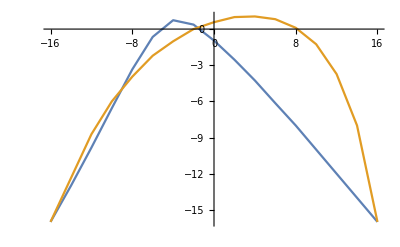

```mathematica
ListLinePlot[{energyflowA110,energyflowA30}]
```

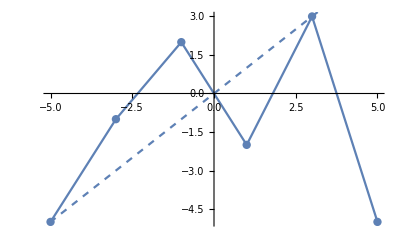

```mathematica
Show[ListLinePlot[Mean/@SortBy[GatherBy[energyflow,First],First],PlotRange->All,Mesh->Full],Plot[x,{x,-100,100},PlotStyle->Dashed]]
```

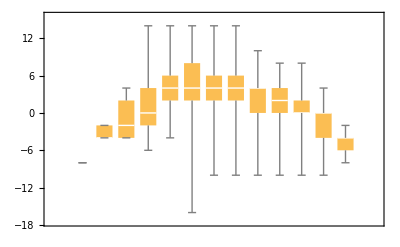

```mathematica
BoxWhiskerChart[#ᵀ⟦2⟧&/@SortBy[GatherBy[energyflow,First],First]]
```

```mathematica
ArrayPlot[CellularAutomaton[27,RandomInteger[{0,1},100],100]]
```

-Graphics-